Jonas Neundorf, Jan Skottke

# Blatt 8 -- Raumladungsarbeitspunktverschiebung

Zunächst berechnen wir aus den Maxwell-Gleichungen in Integralform das elektrische Feld

```mathematica
lefte:=Integrate[Integrate[r*eField,{ϕ,0,2*Pi}],{z,0,l}]
```

```mathematica
righte:=Integrate[Integrate[Integrate[1/ϵ0*r*ρ,{z,0,l}],{ϕ,0,2*Pi}],{r,0,r}]
```

```mathematica
ef=Solve[lefte==righte,eField]//Flatten
```

{eField→(r ρ)/(2 ϵ0)}

und das Magnetfeld.

```mathematica
leftb:=Integrate[r*bField,{ϕ,0,2*Pi}]
```

```mathematica
rightb:=Integrate[Integrate[μ0*r*j,{ϕ,0,2*Pi}],{r,0,r}]
```

```mathematica
bf=Solve[leftb==rightb,bField]//.j-> ρ*β*c//.μ0-> 1/(ϵ0*c^2)//Flatten
```

{bField→(r β ρ)/(2 c ϵ0)}

Damit lässt sich nun ein Ausdruck für die Lorentzkraft aufstellen0

```mathematica
fLorentz[r_]:=(e*(eField+β*c*bField))
```

```mathematica
fLorentz[r]//.ef//.bf//.(1+β^2)-> 1/γ^2//FullSimplify
```

(e r (1+β^2) ρ)/(2 ϵ0)

und die Quadrupolstärke des selbsterzeugten Magnetfeldes berechnen. Anders als beim Quadrupol erzeugt der Strahl auch ein elektrisches Feld, das ihn beeinflusst. Wir müssen also beide Felder bei der Berechnung des Gradienten g berücksichtigen.

```mathematica
g= -1/(e*c*β)D[fLorentz[r] //.bf //.ef, r] //FullSimplify
```

-((1+β^2) ρ)/(2 c β ϵ0)

```mathematica
k = (e*c)/(β*energy)*g//.energy-> m0*c^2*γ //.ρ->i/(π*a^2*β*c)
```

-(e i (1+β^2))/(2 a^2 c^3 m0 π β^3 γ ϵ0)

Betrachten wir nun die Auswirkungen während eines Umlaufes

```mathematica
mQ[l_] := {{1, 0}, {-(k*l), 1}}
```

```mathematica
twissMat:= Cos[μph0]*{{1, 0}, {0, 1}} + Sin[μph0]*{{α, βt}, {-γt, -α}}
```

```mathematica
disturbedMat=twissMat.mQ[ds]//FullSimplify
```

{{Cos[μph0]+α Sin[μph0]+(ds e i (1+β^2) βt Sin[μph0])/(2 a^2 c^3 m0 π β^3 γ ϵ0),βt Sin[μph0]},{-γt Sin[μph0]+(ds e i (1+β^2) (Cos[μph0]-α Sin[μph0]))/(2 a^2 c^3 m0 π β^3 γ ϵ0),Cos[μph0]-α Sin[μph0]}}

Der Phasenvorschub ändert sich um eine kleine Zahl δμ

```mathematica
eq= Cos[μph]==1/2*Tr[disturbedMat]//.μph-> δμ+μph0//FullSimplify
```

Cos[δμ+μph0]==Cos[μph0]+(ds e i (1+β^2) βt Sin[μph0])/(4 a^2 c^3 m0 π β^3 γ ϵ0)

Wir können nun eine Reihenentwicklung um δμ machen. Da die Phasenvorschubsverschiebung pro Umlauf klein sein sollte, reicht es, die Entwicklung nur bis zum linearen Term durchzuführen.

```mathematica
solution=Series[eq,{δμ,0,1}]//Normal
```

Cos[μph0]-δμ Sin[μph0]==Cos[μph0]+(ds e i (1+β^2) βt Sin[μph0])/(4 a^2 c^3 m0 π β^3 γ ϵ0)

```mathematica
phaseshift=Solve[solution,δμ]//Flatten
```

{δμ→-(ds e i (1+β^2) βt)/(4 a^2 c^3 m0 π β^3 γ ϵ0)}

```mathematica
tuneshift=Integrate[δμ/(2*Pi)//.phaseshift,{s,0,l}]//.ds-> 1//.a->Sqrt[ ϵt*βt]//.ϵt-> ϵn/(β*γ)//.(1+β^2)->1/γ^2
```

-(e i l)/(8 c^3 m0 π^2 β^2 γ^2 ϵ0 ϵn)

Bei gleichem γ ist die Arbeitspunktverschiebung für Protonen augrund der höheren Masse um den Faktor 1836 kleiner.

```mathematica
tuneshift //. {γ->ekin/m0+1, β->1-1/γ^2} //FullSimplify
```

-(e i l m0 (ekin+m0)^2)/(8 c^3 ekin^2 (ekin+2 m0)^2 π^2 ϵ0 ϵn)

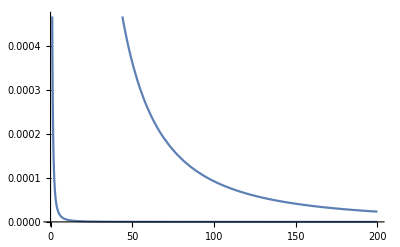

```mathematica
Plot[{(mp(ekin+mp)^2)/(ekin^2(ekin+2mp)^2), (me(ekin+me)^2)/(ekin^2(ekin+2me)^2)}//.{mp->0.938, me->511*10^-6},{ekin, 0, 200}, PlotLegends->"Expressions"]
```

Bei Gleichheit der sonstigen Parameter ist für Protonen die Arbeitspunktverschiebung Aufgrund der höheren Masse stets höher als für Elektronen.

Um den wahren Arbeitspunkt zu messen, müsste man an mehreren Punkten die Phase der Betatronschwingung messen. Da allerdings die einzelnen Teilchen nicht in Phase schwingen, scheidet dieser Weg aus.

Einsetzen der Teilchenzahl

```mathematica
tuneshiftN= tuneshift //.{i->charge/time, charge->e*n, time -> (π*2*R)/(β*c),m0-> (ekin+m)/γ}(*benutzte m um unendliche Rekursion zu vermeiden*)
```

-(e^2 l n)/(16 c^2 (ekin+m) π^3 R β γ ϵ0 ϵn)

```mathematica
equation=δQ== tuneshiftN
```

δQ==-(e^2 l n)/(16 c^2 (ekin+m) π^3 R β γ ϵ0 ϵn)

```mathematica
params={ekin-> 50,R-> 50,m->938.27,e-> 1.602*10^-19,c-> 3.*10^8,β-> 1-1/γ^2,γ->ekin/m ,ϵn-> 10*Pi*10^-6,ϵ0-> 8.85419*10^-12,l-> 50,δQ-> 0.2};
```

```mathematica
Solve[equation//.params,n]//Flatten
```

{n→1.78984×10^45}

```mathematica
1.7*10^45*938.6*(e*10^6)/c^2//.params
```

2.8402×10^18

Die ermittelte maximale Protonenzahl entspricht einer Masse von 3*10^18kg, kann also nicht einmal ansatzweise in den Beschleuniger eingefüllt werden.